```mathematica
Computational Physics, Dr. Dell
September 11, 2013
Didi Chang-Park
```

```mathematica
(* Constant acceleration *)
```

```mathematica
s=Manipulate[StreamPlot[{v,a},{x,-5,5},{v,-5,5}, Axes->True],{{a,0.0},-3,3}]
```

RowBox[{"StreamPlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a stream plot of the vector field RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["y", "TI"]]}], "}"}] as a function of StyleBox["x", "TI"] and StyleBox["y", "TI"]. 
RowBox[{"StreamPlot", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["w", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates plots of several vector fields.

Attributes[StreamPlot]={HoldAll,Protected,ReadProtected}
 
Options[StreamPlot]={AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→None,BoxRatios→Automatic,ColorFunction→None,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},LightingAngle→None,MaxRecursion→Automatic,Mesh→None,MeshFunctions→Automatic,MeshShading→None,MeshStyle→Automatic,Method→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotRange→{Full,Full},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,StreamColorFunction→None,StreamColorFunctionScaling→True,StreamPoints→Automatic,StreamScale→Automatic,StreamStyle→Automatic,Ticks→Automatic,TicksStyle→{},VectorColorFunction→None,VectorColorFunctionScaling→True,VectorPoints→None,VectorScale→Automatic,VectorStyle→Automatic,WorkingPrecision→MachinePrecision}

```mathematica
(* F=-kx *) 

s1 = Manipulate[
StreamPlot[{v,-kbym x},{x,-5,5},{v,-5,5}, StreamPoints -> Fine],
 {{kbym,0.0}, -3, 3}]
```

```mathematica
(* Look at NDSolve tutorials *)
```

```mathematica
?? NDSolve
```

NDSolve[eqns,u,{t,t_min,t_max}] finds a numerical solution to the ordinary differential equations eqns for the function u with the independent variable t in the range t_min to t_max. 
NDSolve[eqns,u,{t,t_min,t_max},{x,x_min,x_max}] finds a numerical solution to the partial differential equations eqns. 
NDSolve[eqns,{u_1,u_2,…},{t,t_min,t_max}] finds numerical solutions for the functions u_i.

Attributes[NDSolve]={Protected}
 
Options[NDSolve]={AccuracyGoal→Automatic,Compiled→Automatic,DependentVariables→Automatic,DiscreteVariables→{},EvaluationMonitor→None,InterpolationOrder→Automatic,MaxStepFraction→1/10,MaxSteps→10000,MaxStepSize→Automatic,Method→Automatic,NormFunction→Automatic,PrecisionGoal→Automatic,StartingStepSize→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}

```mathematica
(*Solve differential equations with constant a, plot*)
```

```mathematica
sol1= NDSolve[{v'[t]== 2.0, x'[t]==v[t],x[0]== 1.0,v[0]== 1.0},{x,v},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
(* Forms square root function *)
```

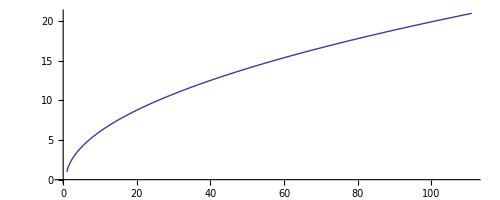

```mathematica
ParametricPlot[{x[t], v[t]}/.First[sol1], {t, 0, 10}]
```

```mathematica
September 12 2013
```

```mathematica
(*  F=-kx *)
```

```mathematica
sol2 = NDSolve[{v'[t]==-1.0x[t], x'[t]==v[t], x[0]==1.0,v[0]==1.0},{x,v},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}

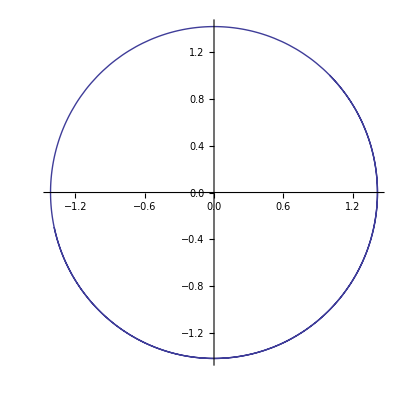

```mathematica
ParametricPlot[{x[t],v[t]}/.First[sol2], {t,0,10}]
```

```mathematica
s = NDSolve[{v'[t]==-4x[t], x'[t]==v[t], x[0]==0, v[0]==1.0},{x,v},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
(*Trying to manipulate initial conditions *)
```

```mathematica
Manipulate[ParametricPlot[{x[t],v[t]}/.First[NDSolve[{v'[t]==2.0, x'[t]==v[t], x[0]==a, v[0]==b},{x,v},{t,0,10}]], {t,0,10}],{a,1,3},{b,1,3}]
```

NDSolve::dsvar: 0.000204082 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0] == 1v[0] == 1 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0.`] == 1.`v[0.`] == 1.` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0] == 1v[0] == 1 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.408367 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

NDSolve::dsvar: 0.000204082 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0] == 1v[0] == 1 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0.`] == 1.`v[0.`] == 1.` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0] == 1v[0] == 1 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.000204082 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0] == 1v[0] == 1 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0.`] == 1.`v[0.`] == 1.` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0] == 1v[0] == 1 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.000204082 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0] == 1v[0] == 1 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0.`] == 1.`v[0.`] == 1.` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0] == 1v[0] == 1 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.000204082 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0] == 1v[0] == 1 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0.`] == 1.`v[0.`] == 1.` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0] == 1v[0] == 1 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.408367 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

NDSolve::dsvar: 0.000204082 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0] == 1v[0] == 1 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0.`] == 1.`v[0.`] == 1.` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0] == 1v[0] == 1 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.408367 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

NDSolve::dsvar: 0.000204082 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0] == 1v[0] == 1 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0.`] == 1.`v[0.`] == 1.` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0] == 1v[0] == 1 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.408367 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

```mathematica
(*WOAH*)
```

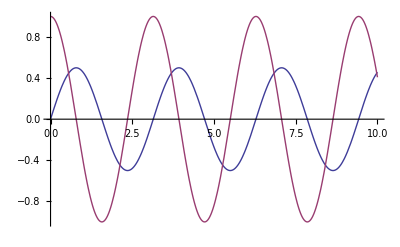

```mathematica
Plot[{  x[t]/.First[s], v[t]/.First[s]},{t,0,10}]
```

```mathematica
s1 = NDSolve[{v'[t]==-4x[t], x'[t]==v[t], x[0]==0, v[0]==0.0},{x,v},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
s2= NDSolve[{v'[t]==-4x[t], x'[t]==v[t], x[0]==0.5, v[0]==0.5},{x,v},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
Table[NDSolve[{v'[t]==-4x[t], x'[t]==v[t],x[0]==i,v[0]==j},{x,v},{t,0,10}],{i,2},{j,i}]
```

{{{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}},{{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}},{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}}}

```mathematica
(*Hooray. A function which produces functions.*)
```

```mathematica
f[a_, b_]:= NDSolve[{v'[t]==-4x[t], x'[t]==v[t],x[0]==a,v[0]==b},{x,v},{t,0,10}]
```

```mathematica
x[t]/.First[s2]
```

{}

```mathematica
x[t]/.First[f[0.5,0.5]]
```

NDSolve::derlen: The length of the derivative operator Derivative[1] in SuperscriptBox[ is not the same as the number of arguments.

ReplaceAll::reps: SuperscriptBox[SuperscriptBox[x[0] == 0.5`v[0] == 0.5` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x[{}]/.{v'[{}]==-4 x[{}],x'[{}]==v[{}],x[0]==0.5,v[0]==0.5}

```mathematica
(*And not so useful. maybe. *)
```

```mathematica
xg[a_,b_]:=x[t]/.First[f[a,b]]
```

```mathematica
xg[0.5,0.5]
```

InterpolatingFunction[{{0.,10.}},<>][t]

```mathematica
vg[a_,b_]:=v[t]/.First[f[a,b]]
```

{x[{}]/.{v'[{}]==-4 x[{}],x'[{}]==v[{}],x[0]==0.5,v[0]==0.5},v[{}]/.{v'[{}]==-4 x[{}],x'[{}]==v[{}],x[0]==0.5,v[0]==0.5}}

```mathematica
Table[v[t]/.First[f[x0,v0]],{x0,5,0.5},{v0,5,0.5}]
```

{}

```mathematica
Manipulate[
Animate[
Graphics[
Point[{{x[t]/.First[f[0,v0]],v[t]/.First[f[0,v0]]}}
		],PlotRange->{{-2,2},{-2,2}}
			], {t,0,6}, AnimationRunning->False],
	{v0,5,0.5}]
```

```mathematica
l = {{x[t]/.First[s],v[t]/.First[s]},{x[t]/.First[s1],v[t]/.First[s1]},{x[t]/.First[s2],v[t]/.First[s2]}};
```

```mathematica
(*Need to draw trajectories for all possible initial conditions. *well, maybe 0.5 steps or something
Start with fixed acceleration function
How to do this:
	-Use table
   - *)
```

```mathematica
Animate[
	Graphics[
		Point[
			      {
				{x[t]/.First[s],v[t]/.First[s]},{x[t]/.First[s1],v[t]/.First[s1]},
                                     {x[t]/.First[s2],v[t]/.First[s2]}
			    }
			]		
		,PlotRange->{{-2,2},{-2,2}}
			],{t,0,6},AnimationRunning->False]
```